# Пререшаване - Вариант 3, Задача 4, фак. номер 2001261003

a = 0, b = 3

Дадена е началната задача за ОДУ:

y' = y - ln(x^2 + 1) + (2x)/(x^2 + 1) + b, y(a) = a + b, x ∈ [a; a + 1]

1. Да се намерят точните решения.
2. Да се решат по методите: Ойлер, модифициран Ойлер, Рунге-Кута (1, 1), Рунге-Кута (2/3, 2/3), Рунге-Кута с 4 междинни точки за а) при h = 0.1, 
за б) при n = 5. Да се направи сравнение между точното решение и численото приближение. Да се представи геометрична интерпретация на резултатите.
3. Колко би трябвало да са n и h за всеки един от посочените методи за всяка от задачите, за да се достигне точност за а) 10^-4, за б) 10^-7?

## А) Да се намери точното решение на задачата

Търсим общо решение:

```mathematica
Clear[x, y]
DSolve[y'[x] ==y[x] - Log[x^2 + 1] + (2x)/(x^2 + 1) + 3, y[x], x]
```

{{y[x]→-3+ⅇ^x C[1]+Log[1+x^2]}}

Търсим точно решение:

```mathematica
Clear[x, y]
DSolve[{y'[x] ==y[x] - Log[x^2 + 1] + (2x)/(x^2 + 1) + 3, y[0] == 3}, y[x], x]
```

{{y[x]→-3+6 ⅇ^x+Log[1+x^2]}}

Визуализация на точното решение

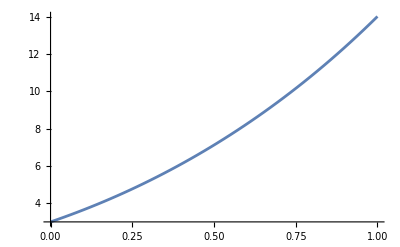

```mathematica
yt[x_] := -3+6 ⅇ^x+Log[1+x^2]
Plot[yt[x], {x,0,1}]
```

## Б) По метод на Рунге - Кута с 4 междинни точки да се реши приближено задачата със стъпка h = 0.02. Запишете резултатите в таблица. Сравнете с точното решение.

#### Метод на Рунге-Кута с 4 междинни точки

Мрежата е с n = 50. и стъпка h = 0.02

Теоретичната локална грешка  е 3.2×10^-9

Теоретичната глобална грешка е 1.6×10^-7

i = 0 x_i = 0. y_i = 3. f_i = 6. k_1 = 0.12 k_2 = 0.121598 k_3 = 0.121614 k_4 = 0.123224 y_точно = 3. Истинска грешка = 0.

i = 1 x_i = 0.02 y_i = 3.12161 f_i = 6.16119 k_1 = 0.123224 k_2 = 0.124845 k_3 = 0.124862 k_4 = 0.126495 y_точно = 3.12161 Истинска грешка = 1.58582×10^-10

i = 2 x_i = 0.04 y_i = 3.24646 f_i = 6.32474 k_1 = 0.126495 k_2 = 0.128139 k_3 = 0.128156 k_4 = 0.129812 y_точно = 3.24646 Истинска грешка = 3.2136×10^-10

i = 3 x_i = 0.06 y_i = 3.37461 f_i = 6.49059 k_1 = 0.129812 k_2 = 0.131479 k_3 = 0.131496 k_4 = 0.133174 y_точно = 3.37461 Истинска грешка = 4.88952×10^-10

i = 4 x_i = 0.08 y_i = 3.5061 f_i = 6.6587 k_1 = 0.133174 k_2 = 0.134864 k_3 = 0.13488 k_4 = 0.136581 y_точно = 3.5061 Истинска грешка = 6.62045×10^-10

i = 5 x_i = 0.1 y_i = 3.64098 f_i = 6.82905 k_1 = 0.136581 k_2 = 0.138292 k_3 = 0.138309 k_4 = 0.140032 y_точно = 3.64098 Истинска грешка = 8.41371×10^-10

i = 6 x_i = 0.12 y_i = 3.77928 f_i = 7.00157 k_1 = 0.140031 k_2 = 0.141764 k_3 = 0.141782 k_4 = 0.143525 y_точно = 3.77928 Истинска грешка = 1.02771×10^-9

i = 7 x_i = 0.14 y_i = 3.92105 f_i = 7.17626 k_1 = 0.143525 k_2 = 0.145279 k_3 = 0.145297 k_4 = 0.147062 y_точно = 3.92105 Истинска грешка = 1.22185×10^-9

i = 8 x_i = 0.16 y_i = 4.06634 f_i = 7.35308 k_1 = 0.147062 k_2 = 0.148837 k_3 = 0.148854 k_4 = 0.15064 y_точно = 4.06634 Истинска грешка = 1.42463×10^-9

i = 9 x_i = 0.18 y_i = 4.21519 f_i = 7.53201 k_1 = 0.15064 k_2 = 0.152436 k_3 = 0.152454 k_4 = 0.154261 y_точно = 4.21519 Истинска грешка = 1.63684×10^-9

i = 10 x_i = 0.2 y_i = 4.36764 f_i = 7.71303 k_1 = 0.154261 k_2 = 0.156077 k_3 = 0.156096 k_4 = 0.157923 y_точно = 4.36764 Истинска грешка = 1.85928×10^-9

i = 11 x_i = 0.22 y_i = 4.52373 f_i = 7.89615 k_1 = 0.157923 k_2 = 0.159761 k_3 = 0.159779 k_4 = 0.161627 y_точно = 4.52373 Истинска грешка = 2.09274×10^-9

i = 12 x_i = 0.24 y_i = 4.6835 f_i = 8.08135 k_1 = 0.161627 k_2 = 0.163485 k_3 = 0.163504 k_4 = 0.165373 y_точно = 4.6835 Истинска грешка = 2.33795×10^-9

i = 13 x_i = 0.26 y_i = 4.84699 f_i = 8.26865 k_1 = 0.165373 k_2 = 0.167252 k_3 = 0.167271 k_4 = 0.169161 y_точно = 4.84699 Истинска грешка = 2.59559×10^-9

i = 14 x_i = 0.28 y_i = 5.01426 f_i = 8.45807 k_1 = 0.169161 k_2 = 0.171062 k_3 = 0.171081 k_4 = 0.172992 y_точно = 5.01426 Истинска грешка = 2.86632×10^-9

i = 15 x_i = 0.3 y_i = 5.18533 f_i = 8.64961 k_1 = 0.172992 k_2 = 0.174914 k_3 = 0.174933 k_4 = 0.176867 y_точно = 5.18533 Истинска грешка = 3.15071×10^-9

i = 16 x_i = 0.32 y_i = 5.36026 f_i = 8.84332 k_1 = 0.176866 k_2 = 0.17881 k_3 = 0.17883 k_4 = 0.180785 y_точно = 5.36026 Истинска грешка = 3.44929×10^-9

i = 17 x_i = 0.34 y_i = 5.53908 f_i = 9.03922 k_1 = 0.180784 k_2 = 0.18275 k_3 = 0.18277 k_4 = 0.184748 y_точно = 5.53908 Истинска грешка = 3.76252×10^-9

i = 18 x_i = 0.36 y_i = 5.72184 f_i = 9.23737 k_1 = 0.184747 k_2 = 0.186736 k_3 = 0.186756 k_4 = 0.188756 y_точно = 5.72184 Истинска грешка = 4.09081×10^-9

i = 19 x_i = 0.38 y_i = 5.90859 f_i = 9.43781 k_1 = 0.188756 k_2 = 0.190768 k_3 = 0.190788 k_4 = 0.192812 y_точно = 5.90859 Истинска грешка = 4.43448×10^-9

i = 20 x_i = 0.4 y_i = 6.09937 f_i = 9.6406 k_1 = 0.192812 k_2 = 0.194848 k_3 = 0.194868 k_4 = 0.196916 y_точно = 6.09937 Истинска грешка = 4.79385×10^-9

i = 21 x_i = 0.42 y_i = 6.29423 f_i = 9.84581 k_1 = 0.196916 k_2 = 0.198977 k_3 = 0.198997 k_4 = 0.20107 y_точно = 6.29423 Истинска грешка = 5.16914×10^-9

i = 22 x_i = 0.44 y_i = 6.49322 f_i = 10.0535 k_1 = 0.20107 k_2 = 0.203156 k_3 = 0.203177 k_4 = 0.205276 y_точно = 6.49322 Истинска грешка = 5.56056×10^-9

i = 23 x_i = 0.46 y_i = 6.69639 f_i = 10.2638 k_1 = 0.205275 k_2 = 0.207387 k_3 = 0.207408 k_4 = 0.209534 y_точно = 6.69639 Истинска грешка = 5.96826×10^-9

i = 24 x_i = 0.48 y_i = 6.90379 f_i = 10.4767 k_1 = 0.209534 k_2 = 0.211672 k_3 = 0.211694 k_4 = 0.213847 y_точно = 6.90379 Истинска грешка = 6.39238×10^-9

i = 25 x_i = 0.5 y_i = 7.11547 f_i = 10.6923 k_1 = 0.213847 k_2 = 0.216013 k_3 = 0.216035 k_4 = 0.218216 y_точно = 7.11547 Истинска грешка = 6.83303×10^-9

i = 26 x_i = 0.52 y_i = 7.3315 f_i = 10.9108 k_1 = 0.218216 k_2 = 0.220412 k_3 = 0.220434 k_4 = 0.222644 y_точно = 7.3315 Истинска грешка = 7.29029×10^-9

i = 27 x_i = 0.54 y_i = 7.55192 f_i = 11.1322 k_1 = 0.222644 k_2 = 0.22487 k_3 = 0.224892 k_4 = 0.227133 y_точно = 7.55192 Истинска грешка = 7.76427×10^-9

i = 28 x_i = 0.56 y_i = 7.77681 f_i = 11.3567 k_1 = 0.227133 k_2 = 0.22939 k_3 = 0.229412 k_4 = 0.231685 y_точно = 7.77681 Истинска грешка = 8.25503×10^-9

i = 29 x_i = 0.58 y_i = 8.00621 f_i = 11.5842 k_1 = 0.231685 k_2 = 0.233973 k_3 = 0.233996 k_4 = 0.236301 y_точно = 8.00621 Истинска грешка = 8.76267×10^-9

i = 30 x_i = 0.6 y_i = 8.2402 f_i = 11.8151 k_1 = 0.236301 k_2 = 0.238623 k_3 = 0.238646 k_4 = 0.240985 y_точно = 8.2402 Истинска грешка = 9.28729×10^-9

i = 31 x_i = 0.62 y_i = 8.47884 f_i = 12.0493 k_1 = 0.240985 k_2 = 0.243341 k_3 = 0.243365 k_4 = 0.245739 y_точно = 8.47884 Истинска грешка = 9.82899×10^-9

i = 32 x_i = 0.64 y_i = 8.72219 f_i = 12.2869 k_1 = 0.245739 k_2 = 0.248131 k_3 = 0.248154 k_4 = 0.250565 y_точно = 8.72219 Истинска грешка = 1.03879×10^-8

i = 33 x_i = 0.66 y_i = 8.97034 f_i = 12.5282 k_1 = 0.250565 k_2 = 0.252993 k_3 = 0.253017 k_4 = 0.255465 y_точно = 8.97034 Истинска грешка = 1.09642×10^-8

i = 34 x_i = 0.68 y_i = 9.22335 f_i = 12.7732 k_1 = 0.255465 k_2 = 0.257931 k_3 = 0.257956 k_4 = 0.260442 y_точно = 9.22335 Истинска грешка = 1.1558×10^-8

i = 35 x_i = 0.7 y_i = 9.48129 f_i = 13.0221 k_1 = 0.260442 k_2 = 0.262948 k_3 = 0.262973 k_4 = 0.2655 y_точно = 9.48129 Истинска грешка = 1.21696×10^-8

i = 36 x_i = 0.72 y_i = 9.74426 f_i = 13.275 k_1 = 0.265499 k_2 = 0.268046 k_3 = 0.268071 k_4 = 0.270639 y_точно = 9.74426 Истинска грешка = 1.27992×10^-8

i = 37 x_i = 0.74 y_i = 10.0123 f_i = 13.5319 k_1 = 0.270639 k_2 = 0.273227 k_3 = 0.273253 k_4 = 0.275863 y_точно = 10.0123 Истинска грешка = 1.3447×10^-8

i = 38 x_i = 0.76 y_i = 10.2856 f_i = 13.7931 k_1 = 0.275863 k_2 = 0.278495 k_3 = 0.278521 k_4 = 0.281175 y_точно = 10.2856 Истинска грешка = 1.41134×10^-8

i = 39 x_i = 0.78 y_i = 10.5641 f_i = 14.0587 k_1 = 0.281175 k_2 = 0.283851 k_3 = 0.283878 k_4 = 0.286577 y_точно = 10.5641 Истинска грешка = 1.47987×10^-8

i = 40 x_i = 0.8 y_i = 10.8479 f_i = 14.3289 k_1 = 0.286577 k_2 = 0.289299 k_3 = 0.289327 k_4 = 0.292073 y_точно = 10.8479 Истинска грешка = 1.55032×10^-8

i = 41 x_i = 0.82 y_i = 11.1373 f_i = 14.6036 k_1 = 0.292073 k_2 = 0.294842 k_3 = 0.29487 k_4 = 0.297664 y_точно = 11.1373 Истинска грешка = 1.62274×10^-8

i = 42 x_i = 0.84 y_i = 11.4321 f_i = 14.8832 k_1 = 0.297664 k_2 = 0.300482 k_3 = 0.30051 k_4 = 0.303354 y_точно = 11.4321 Истинска грешка = 1.69716×10^-8

i = 43 x_i = 0.86 y_i = 11.7326 f_i = 15.1677 k_1 = 0.303354 k_2 = 0.306223 k_3 = 0.306251 k_4 = 0.309146 y_точно = 11.7326 Истинска грешка = 1.77364×10^-8

i = 44 x_i = 0.88 y_i = 12.0389 f_i = 15.4573 k_1 = 0.309146 k_2 = 0.312066 k_3 = 0.312095 k_4 = 0.315042 y_точно = 12.0389 Истинска грешка = 1.85222×10^-8

i = 45 x_i = 0.9 y_i = 12.3509 f_i = 15.7521 k_1 = 0.315042 k_2 = 0.318015 k_3 = 0.318045 k_4 = 0.321046 y_точно = 12.3509 Истинска грешка = 1.93295×10^-8

i = 46 x_i = 0.92 y_i = 12.669 f_i = 16.0523 k_1 = 0.321046 k_2 = 0.324073 k_3 = 0.324104 k_4 = 0.32716 y_точно = 12.669 Истинска грешка = 2.0159×10^-8

i = 47 x_i = 0.94 y_i = 12.9931 f_i = 16.358 k_1 = 0.32716 k_2 = 0.330243 k_3 = 0.330274 k_4 = 0.333387 y_точно = 12.9931 Истинска грешка = 2.10111×10^-8

i = 48 x_i = 0.96 y_i = 13.3233 f_i = 16.6693 k_1 = 0.333387 k_2 = 0.336528 k_3 = 0.33656 k_4 = 0.339731 y_точно = 13.3233 Истинска грешка = 2.18865×10^-8

i = 49 x_i = 0.98 y_i = 13.6599 f_i = 16.9865 k_1 = 0.339731 k_2 = 0.342931 k_3 = 0.342963 k_4 = 0.346194 y_точно = 13.6599 Истинска грешка = 2.27859×10^-8

i = 50 x_i = 1. y_i = 14.0028 f_i = 17.3097 k_1 = 0.346194 k_2 = 0.349455 k_3 = 0.349487 k_4 = 0.35278 y_точно = 14.0028 Истинска грешка = 2.37099×10^-8

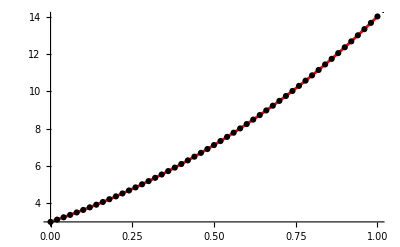

```mathematica
(*Въвеждаме услонието на задачата*)
a = 0.; b = 1.;
x = a;
y = 3.;
points = {{x,y}};
f[x_,y_]:=y - Log[x^2+1]+(2x)/(x^2+1)+3
(*точно решение*)
yt[x_]:=-3+6 ⅇ^x+Log[1+x^2]
(*Съставяме мрежата*)
h = 0.02; n = (b - a)/h;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
k1 = h *  f[x,y];
k2 = h *  f[x + h/2,y + k1/2];
k3 = h *  f[x + h/2,y + k2/2];
k4 = h *  f[x + h,y + k3];
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y]  , " k_1 = ", k1, " k_2 = ", k2, " k_3 = ", k3, " k_4 = ", k4, " y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y +1/6(k1 + 2k2 + 2k3 + k4);
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a, b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt, grp]
```

Отговор: В таблицата да се препишат i, x_i, y_i, y_точно, истинска грешка.

## в) Каква е теоретичната грешка на полученото приближено решение?

Отговор: Да се препишат теоретичната локална и глобална грешка.

## г) Каква би била точността при използване на модифицирания метод на Ойлер със същата стъпка (h = 0.02)? Направете сравнение между двата метода

#### Модифициран метод на Ойлер

Мрежата е с n = 50. и стъпка h = 0.02

Теоретичната локална грешка  е 8.×10^-6

Теоретичната глобална грешка е 0.0004

i = 0 x_i = 0. y_i = 3. f_i = 6. x_(i + 1/2) = 0.01 y_(i + 1/2) = 3.06 f_(i + 1/2) = 6.0799  y_точно = 3. Истинска грешка = 0.

i = 1 x_i = 0.02 y_i = 3.1216 f_i = 6.16118 x_(i + 1/2) = 0.03 y_(i + 1/2) = 3.18321 f_(i + 1/2) = 6.24226  y_точно = 3.12161 Истинска грешка = 0.0000100001

i = 2 x_i = 0.04 y_i = 3.24644 f_i = 6.32472 x_(i + 1/2) = 0.05 y_(i + 1/2) = 3.30969 f_(i + 1/2) = 6.40694  y_точно = 3.24646 Истинска грешка = 0.0000202817

i = 3 x_i = 0.06 y_i = 3.37458 f_i = 6.49056 x_(i + 1/2) = 0.07 y_(i + 1/2) = 3.43949 f_(i + 1/2) = 6.57392  y_точно = 3.37461 Истинска грешка = 0.0000308501

i = 4 x_i = 0.08 y_i = 3.50606 f_i = 6.65866 x_(i + 1/2) = 0.09 y_(i + 1/2) = 3.57265 f_(i + 1/2) = 6.74313  y_точно = 3.5061 Истинска грешка = 0.0000417113

i = 5 x_i = 0.1 y_i = 3.64092 f_i = 6.82899 x_(i + 1/2) = 0.11 y_(i + 1/2) = 3.70921 f_(i + 1/2) = 6.91456  y_точно = 3.64098 Истинска грешка = 0.000052872

i = 6 x_i = 0.12 y_i = 3.77921 f_i = 7.00151 x_(i + 1/2) = 0.13 y_(i + 1/2) = 3.84923 f_(i + 1/2) = 7.08815  y_точно = 3.77928 Истинска грешка = 0.0000643401

i = 7 x_i = 0.14 y_i = 3.92098 f_i = 7.17618 x_(i + 1/2) = 0.15 y_(i + 1/2) = 3.99274 f_(i + 1/2) = 7.26389  y_точно = 3.92105 Истинска грешка = 0.0000761244

i = 8 x_i = 0.16 y_i = 4.06625 f_i = 7.35299 x_(i + 1/2) = 0.17 y_(i + 1/2) = 4.13978 f_(i + 1/2) = 7.44174  y_точно = 4.06634 Истинска грешка = 0.0000882343

i = 9 x_i = 0.18 y_i = 4.21509 f_i = 7.53191 x_(i + 1/2) = 0.19 y_(i + 1/2) = 4.29041 f_(i + 1/2) = 7.62171  y_точно = 4.21519 Истинска грешка = 0.00010068

i = 10 x_i = 0.2 y_i = 4.36752 f_i = 7.71292 x_(i + 1/2) = 0.21 y_(i + 1/2) = 4.44465 f_(i + 1/2) = 7.80376  y_точно = 4.36764 Истинска грешка = 0.000113474

i = 11 x_i = 0.22 y_i = 4.5236 f_i = 7.89602 x_(i + 1/2) = 0.23 y_(i + 1/2) = 4.60256 f_(i + 1/2) = 7.9879  y_точно = 4.52373 Истинска грешка = 0.000126627

i = 12 x_i = 0.24 y_i = 4.68336 f_i = 8.08121 x_(i + 1/2) = 0.25 y_(i + 1/2) = 4.76417 f_(i + 1/2) = 8.17413  y_точно = 4.6835 Истинска грешка = 0.000140154

i = 13 x_i = 0.26 y_i = 4.84684 f_i = 8.2685 x_(i + 1/2) = 0.27 y_(i + 1/2) = 4.92952 f_(i + 1/2) = 8.36247  y_точно = 4.84699 Истинска грешка = 0.000154067

i = 14 x_i = 0.28 y_i = 5.01409 f_i = 8.4579 x_(i + 1/2) = 0.29 y_(i + 1/2) = 5.09867 f_(i + 1/2) = 8.55292  y_точно = 5.01426 Истинска грешка = 0.000168381

i = 15 x_i = 0.3 y_i = 5.18515 f_i = 8.64943 x_(i + 1/2) = 0.31 y_(i + 1/2) = 5.27164 f_(i + 1/2) = 8.74553  y_точно = 5.18533 Истинска грешка = 0.000183112

i = 16 x_i = 0.32 y_i = 5.36006 f_i = 8.84312 x_(i + 1/2) = 0.33 y_(i + 1/2) = 5.44849 f_(i + 1/2) = 8.94031  y_точно = 5.36026 Истинска грешка = 0.000198275

i = 17 x_i = 0.34 y_i = 5.53886 f_i = 9.03901 x_(i + 1/2) = 0.35 y_(i + 1/2) = 5.62925 f_(i + 1/2) = 9.1373  y_точно = 5.53908 Истинска грешка = 0.000213888

i = 18 x_i = 0.36 y_i = 5.72161 f_i = 9.23714 x_(i + 1/2) = 0.37 y_(i + 1/2) = 5.81398 f_(i + 1/2) = 9.33657  y_точно = 5.72184 Истинска грешка = 0.000229967

i = 19 x_i = 0.38 y_i = 5.90834 f_i = 9.43756 x_(i + 1/2) = 0.39 y_(i + 1/2) = 6.00272 f_(i + 1/2) = 9.53816  y_точно = 5.90859 Истинска грешка = 0.00024653

i = 20 x_i = 0.4 y_i = 6.0991 f_i = 9.64034 x_(i + 1/2) = 0.41 y_(i + 1/2) = 6.19551 f_(i + 1/2) = 9.74212  y_точно = 6.09937 Истинска грешка = 0.000263595

i = 21 x_i = 0.42 y_i = 6.29395 f_i = 9.84553 x_(i + 1/2) = 0.43 y_(i + 1/2) = 6.3924 f_(i + 1/2) = 9.94854  y_точно = 6.29423 Истинска грешка = 0.000281182

i = 22 x_i = 0.44 y_i = 6.49292 f_i = 10.0532 x_(i + 1/2) = 0.45 y_(i + 1/2) = 6.59345 f_(i + 1/2) = 10.1575  y_точно = 6.49322 Истинска грешка = 0.000299309

i = 23 x_i = 0.46 y_i = 6.69607 f_i = 10.2635 x_(i + 1/2) = 0.47 y_(i + 1/2) = 6.7987 f_(i + 1/2) = 10.369  y_точно = 6.69639 Истинска грешка = 0.000317996

i = 24 x_i = 0.48 y_i = 6.90345 f_i = 10.4763 x_(i + 1/2) = 0.49 y_(i + 1/2) = 7.00821 f_(i + 1/2) = 10.5833  y_точно = 6.90379 Истинска грешка = 0.000337263

i = 25 x_i = 0.5 y_i = 7.11511 f_i = 10.692 x_(i + 1/2) = 0.51 y_(i + 1/2) = 7.22203 f_(i + 1/2) = 10.8003  y_точно = 7.11547 Истинска грешка = 0.000357131

i = 26 x_i = 0.52 y_i = 7.33112 f_i = 10.9104 x_(i + 1/2) = 0.53 y_(i + 1/2) = 7.44022 f_(i + 1/2) = 11.0202  y_точно = 7.3315 Истинска грешка = 0.000377621

i = 27 x_i = 0.54 y_i = 7.55152 f_i = 11.1318 x_(i + 1/2) = 0.55 y_(i + 1/2) = 7.66284 f_(i + 1/2) = 11.2431  y_точно = 7.55192 Истинска грешка = 0.000398753

i = 28 x_i = 0.56 y_i = 7.77639 f_i = 11.3562 x_(i + 1/2) = 0.57 y_(i + 1/2) = 7.88995 f_(i + 1/2) = 11.4691  y_точно = 7.77681 Истинска грешка = 0.00042055

i = 29 x_i = 0.58 y_i = 8.00577 f_i = 11.5838 x_(i + 1/2) = 0.59 y_(i + 1/2) = 8.1216 f_(i + 1/2) = 11.6982  y_точно = 8.00621 Истинска грешка = 0.000443034

i = 30 x_i = 0.6 y_i = 8.23973 f_i = 11.8146 x_(i + 1/2) = 0.61 y_(i + 1/2) = 8.35788 f_(i + 1/2) = 11.9307  y_точно = 8.2402 Истинска грешка = 0.000466226

i = 31 x_i = 0.62 y_i = 8.47834 f_i = 12.0488 x_(i + 1/2) = 0.63 y_(i + 1/2) = 8.59883 f_(i + 1/2) = 12.1666  y_точно = 8.47884 Истинска грешка = 0.00049015

i = 32 x_i = 0.64 y_i = 8.72168 f_i = 12.2864 x_(i + 1/2) = 0.65 y_(i + 1/2) = 8.84454 f_(i + 1/2) = 12.406  y_точно = 8.72219 Истинска грешка = 0.000514829

i = 33 x_i = 0.66 y_i = 8.9698 f_i = 12.5277 x_(i + 1/2) = 0.67 y_(i + 1/2) = 9.09507 f_(i + 1/2) = 12.6491  y_точно = 8.97034 Истинска грешка = 0.000540287

i = 34 x_i = 0.68 y_i = 9.22278 f_i = 12.7727 x_(i + 1/2) = 0.69 y_(i + 1/2) = 9.35051 f_(i + 1/2) = 12.896  y_точно = 9.22335 Истинска грешка = 0.000566548

i = 35 x_i = 0.7 y_i = 9.4807 f_i = 13.0215 x_(i + 1/2) = 0.71 y_(i + 1/2) = 9.61091 f_(i + 1/2) = 13.1468  y_точно = 9.48129 Истинска грешка = 0.000593636

i = 36 x_i = 0.72 y_i = 9.74363 f_i = 13.2743 x_(i + 1/2) = 0.73 y_(i + 1/2) = 9.87638 f_(i + 1/2) = 13.4017  y_точно = 9.74426 Истинска грешка = 0.000621576

i = 37 x_i = 0.74 y_i = 10.0117 f_i = 13.5313 x_(i + 1/2) = 0.75 y_(i + 1/2) = 10.147 f_(i + 1/2) = 13.6607  y_точно = 10.0123 Истинска грешка = 0.000650395

i = 38 x_i = 0.76 y_i = 10.2849 f_i = 13.7925 x_(i + 1/2) = 0.77 y_(i + 1/2) = 10.4228 f_(i + 1/2) = 13.924  y_точно = 10.2856 Истинска грешка = 0.000680116

i = 39 x_i = 0.78 y_i = 10.5634 f_i = 14.058 x_(i + 1/2) = 0.79 y_(i + 1/2) = 10.7039 f_(i + 1/2) = 14.1918  y_точно = 10.5641 Истинска грешка = 0.000710769

i = 40 x_i = 0.8 y_i = 10.8472 f_i = 14.3281 x_(i + 1/2) = 0.81 y_(i + 1/2) = 10.9905 f_(i + 1/2) = 14.4642  y_точно = 10.8479 Истинска грешка = 0.000742378

i = 41 x_i = 0.82 y_i = 11.1365 f_i = 14.6029 x_(i + 1/2) = 0.83 y_(i + 1/2) = 11.2825 f_(i + 1/2) = 14.7413  y_точно = 11.1373 Истинска грешка = 0.000774973

i = 42 x_i = 0.84 y_i = 11.4313 f_i = 14.8824 x_(i + 1/2) = 0.85 y_(i + 1/2) = 11.5801 f_(i + 1/2) = 15.0233  y_точно = 11.4321 Истинска грешка = 0.00080858

i = 43 x_i = 0.86 y_i = 11.7318 f_i = 15.1669 x_(i + 1/2) = 0.87 y_(i + 1/2) = 11.8834 f_(i + 1/2) = 15.3103  y_точно = 11.7326 Истинска грешка = 0.00084323

i = 44 x_i = 0.88 y_i = 12.038 f_i = 15.4564 x_(i + 1/2) = 0.89 y_(i + 1/2) = 12.1925 f_(i + 1/2) = 15.6024  y_точно = 12.0389 Истинска грешка = 0.00087895

i = 45 x_i = 0.9 y_i = 12.35 f_i = 15.7512 x_(i + 1/2) = 0.91 y_(i + 1/2) = 12.5075 f_(i + 1/2) = 15.8998  y_точно = 12.3509 Истинска грешка = 0.000915773

i = 46 x_i = 0.92 y_i = 12.668 f_i = 16.0513 x_(i + 1/2) = 0.93 y_(i + 1/2) = 12.8285 f_(i + 1/2) = 16.2027  y_точно = 12.669 Истинска грешка = 0.000953727

i = 47 x_i = 0.94 y_i = 12.9921 f_i = 16.357 x_(i + 1/2) = 0.95 y_(i + 1/2) = 13.1557 f_(i + 1/2) = 16.5112  y_точно = 12.9931 Истинска грешка = 0.000992845

i = 48 x_i = 0.96 y_i = 13.3223 f_i = 16.6683 x_(i + 1/2) = 0.97 y_(i + 1/2) = 13.489 f_(i + 1/2) = 16.8254  y_точно = 13.3233 Истинска грешка = 0.00103316

i = 49 x_i = 0.98 y_i = 13.6588 f_i = 16.9855 x_(i + 1/2) = 0.99 y_(i + 1/2) = 13.8287 f_(i + 1/2) = 17.1455  y_точно = 13.6599 Истинска грешка = 0.0010747

i = 50 x_i = 1. y_i = 14.0017 f_i = 17.3086 x_(i + 1/2) = 1.01 y_(i + 1/2) = 14.1748 f_(i + 1/2) = 17.4716  y_точно = 14.0028 Истинска грешка = 0.00111751

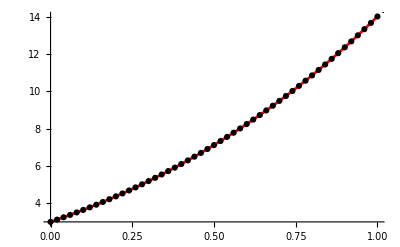

```mathematica
(*Въвеждаме услонието на задачата*)
a = 0.; b = 1.;
x = a;
y = 3.;
points = {{x,y}};
f[x_,y_]:=y - Log[x^2+1]+(2x)/(x^2+1)+3
(*точно решение*)
yt[x_]:=-3+6 ⅇ^x+Log[1+x^2]
(*Съставяме мрежата*)
h = 0.02; n = (b - a)/h;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
x12 = x + h/2;
y12 = y + h/2 f[x,y];
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y]  , " x_(i + 1/2) = ", x12, " y_(i + 1/2) = ", y12, " f_(i + 1/2) = ", f[x12,y12]  " y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y + h*f[x12,y12];
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle-> Black];
Show[gryt, grp]
```

Отговор: При 50 итерации със същата стъпка с метода на Рунге - Кута с 4 междинни точки приближеното решение съвпада с точното с грешка 2.37099×10^-8. При модифицирания метод на Ойлер приближеното решение е 14.0017 с грешка  0.00111751. Следователно метода на Рунге - Кута с 4 междинни точки е по-точен.